```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
singleACCPlot[nam_, dataIn_, colS_]:=Module[{names,namInd,data,head,arrows,points,plot1,dataInset,boxInset},
names={"DLB","MUR","LYE","PHI","SED","AUS"};
namInd=Position[names,nam][[1,1]];
(*Print[namInd];*)
data=If[nam≠"LYE",dataIn[[namInd]][[2]],Drop[dataIn[[namInd]][[2]],{-2}]];
Print["data ", data];

head=Graphics[{Thickness[0.007],Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]}];
arrows=bowedArrowsData[data];

dataInset={{"PERS",ToString[nam]}};
boxInset=Text@Grid[Prepend[dataInset,{"CON"," "}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Left,Center}},ItemSize->{{4,4}},Frame->Darker[Gray,.6],ItemStyle->17,Spacings->{Automatic,.8}];

plot1=Graphics[{Opacity[0.4],colS[[#4]],Arrowheads[{{.012,1,{head,0.01}}}],Thickness[0.007],Arrow[BezierCurve[{#1,#2,#3}]]}&@@@arrows, PlotRange->{{0.5,1.0},{0.5,1.0}},Frame->True,FrameLabel->{Style["CON_e",30],Style["CON_h",30]},ImageSize->800, ImagePadding->120,Epilog->Inset[Style[boxInset,16],{0.62,0.94}]];

Return[plot1];
];

(*{0.7,1.05}*)
```

```mathematica
accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/POINTS/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"]
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue,Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]];
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
revType="ACC"
```

<|DLB→{{0,0.6},{0.5,0.6},{1,0.6},{1.5,0.6},{2,0.6},{2.5,0.6},{3,0.6},{3.5,0.6},{4,0.533333},{4.5,0.533333},{5,0.533333},{5.5,0.533333},{6,0.6},{6.5,0.6},{7,0.6},{7.5,0.6},{8,1.}},MUR→{{1,0.733333},{1.5,0.733333},{2,0.733333},{2.5,0.733333},{3,0.666667},{3.5,0.666667},{4,0.666667},{4.5,0.666667},{5,0.733333},{5.5,0.733333},{6,0.8},{6.5,0.8},{7,1.},{7.5,1.},{8,1.}},LYE→{{1,0.733333},{1.5,0.733333},{2,0.733333},{2.5,0.733333},{3,0.666667},{3.5,0.666667},{4,0.666667},{4.5,0.666667},{5,0.666667},{5.5,0.666667},{6,0.8},{6.5,0.8},{7,1.},{7.5,1.},{8,1.}},PHI→{{2,0.6},{2.5,0.6},{3,0.6},{3.5,0.6},{4,0.8},{4.5,0.8},{5,0.8},{5.5,0.8},{6,0.8},{6.5,0.8},{7,0.8},{7.5,0.8},{8,1.}},SED→{{3,0.666667},{3.5,0.666667},{4,0.8},{4.5,0.8},{5,0.8},{5.5,0.8},{6,0.666667},{6.5,0.666667},{7,0.666667},{7.5,0.666667},{8,1.}},AUS→{{6,0.866667},{6.5,0.866667},{7,0.866667},{7.5,0.866667},{8,1.}}|>

{DLB,MUR,LYE,PHI,SED,AUS}

ACC

data {{0.519231,0.6,1},{0.423077,0.6,2},{0.533333,0.6,3},{0.6,0.6,4},{0.771429,0.6,5},{0.77551,0.6,6},{0.938776,0.6,7},{0.906977,0.6,8},{0.911602,0.533333,9},{0.879581,0.533333,10},{0.889447,0.533333,11},{0.881517,0.533333,12},{0.807175,0.6,13},{0.778723,0.6,14},{0.76569,0.6,15},{0.764259,0.6,16},{0.9631,1.,17}}

data {{0.708333,0.733333,3},{0.716814,0.733333,4},{0.780488,0.733333,5},{0.790698,0.733333,6},{0.84507,0.666667,7},{0.775281,0.666667,8},{0.766667,0.666667,9},{0.727273,0.666667,10},{0.791878,0.733333,11},{0.789474,0.733333,12},{0.709091,0.8,13},{0.698276,0.8,14},{0.934426,1.,15},{0.911111,1.,16},{0.97026,1.,17}}

data {{0.666667,0.733333,3},{0.696429,0.733333,4},{0.756098,0.733333,5},{0.761538,0.733333,6},{0.823944,0.666667,7},{0.792135,0.666667,8},{0.783333,0.666667,9},{0.75,0.666667,10},{0.727723,0.666667,11},{0.728972,0.666667,12},{0.729358,0.8,13},{0.717391,0.8,14},{0.841463,1.,15},{0.966667,1.,17}}

data {{0.860656,0.6,5},{0.860465,0.6,6},{0.914894,0.6,7},{0.885542,0.6,8},{0.908571,0.8,9},{0.875676,0.8,10},{0.88601,0.8,11},{0.878049,0.8,12},{0.861244,0.8,13},{0.841629,0.8,14},{0.84,0.8,15},{0.841897,0.8,16},{0.9631,1.,17}}

data {{0.914894,0.666667,7},{0.885542,0.666667,8},{0.845304,0.8,9},{0.816754,0.8,10},{0.820896,0.8,11},{0.816901,0.8,12},{0.801843,0.666667,13},{0.786026,0.666667,14},{0.803347,0.666667,15},{0.781609,0.666667,16},{0.9631,1.,17}}

data {{0.914798,0.866667,13},{0.901288,0.866667,14},{0.891213,0.866667,15},{0.878327,0.866667,16},{0.9631,1.,17}}

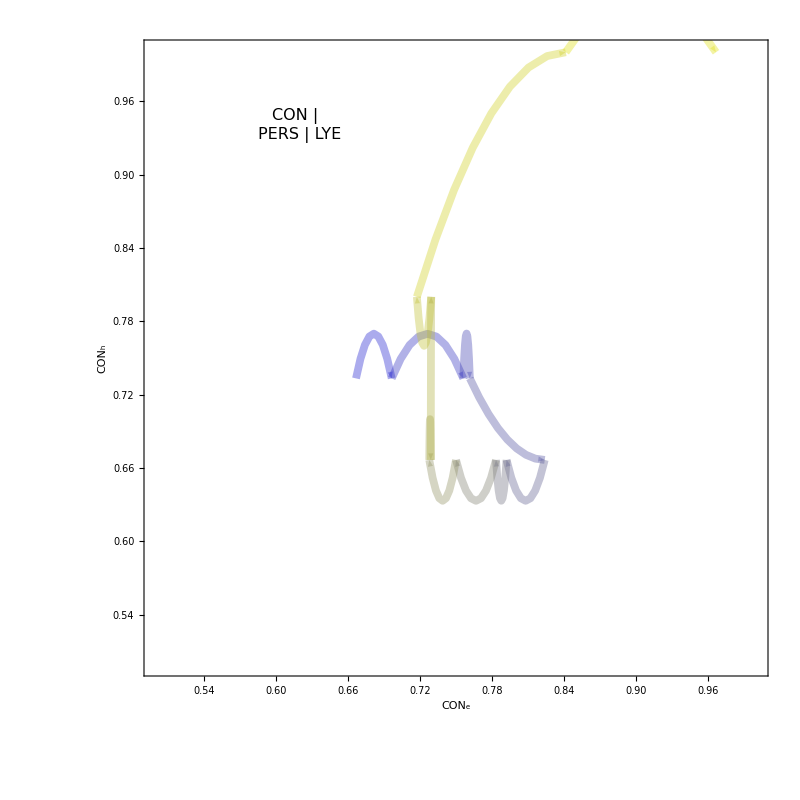

```mathematica
(*{conf,mod, dataConfCircles}*)
data=Map[compACCheFunc[#, accEVBK, accCH, {}]&,names];
plots=Map[singleACCPlot[#, data, col2]&,names];
plots[[3]]
```

```mathematica
plotsGrid=Grid[{plots[[1;;2]],plots[[3;;4]],plots[[5;;6]]}];
```

```mathematica
(*plotsDOJ[[1]]*)
```

```mathematica
dOut=data[[All,3]];

dH=Association@Map[Function[x, 
names[[x]]->Map[Function[y,{y[[3]],y[[2]]}],dOut[[x]]]
],Range[Length[dOut]]];

dE=Association@Map[Function[x, 
names[[x]]->Map[Function[y,{y[[3]],y[[1]]}],dOut[[x]]]
],Range[Length[dOut]]];
```

```mathematica
(*ImageResolution->200*)
SetDirectory[homeAdd<>"/ACC_2"];
Map[Export["ACC_h_ACC_e_"<>ToString[names[[#]]]<>".jpeg",plots[[#]]]&,Range[Length[names]]]
Export["ACC_h_ACC_e.jpeg",plotsGrid]
Put[{dH,dE}, "ACC_h_ACC_e.txt"]
```

{ACC_h_ACC_e_DLB.jpeg,ACC_h_ACC_e_MUR.jpeg,ACC_h_ACC_e_LYE.jpeg,ACC_h_ACC_e_PHI.jpeg,ACC_h_ACC_e_SED.jpeg,ACC_h_ACC_e_AUS.jpeg}

ACC_h_ACC_e.jpeg